```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

109

108

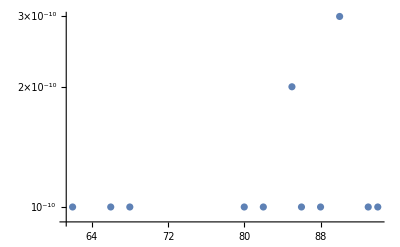

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False
]
```

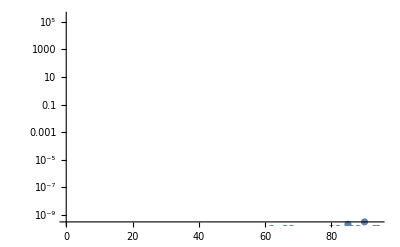

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{2.5*^5,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|S1EL_xOffset→0.00350184,S1EL_yOffset→-0.000976721,S2EL_xOffset→0.000650474,S2EL_yOffset→0.000338885,S2ER_xOffset→0.00208918,S2ER_yOffset→0.000538394,S1ER_xOffset→-0.000141692,S1ER_yOffset→-0.000973673,XC1FFkG→0.151509,XC3FFkG→-0.085597,YC1FFkG→-0.00332671,YC2FFkG→-0.0304129,PDrive_mean_x→0.0000452901,PDrive_mean_y→-0.0000555127,PDrive_sigma_x→0.000208867,PDrive_sigma_y→0.0000668754,PDrive_mean_xp→0.000231949,PDrive_mean_yp→-0.000218626,PDrive_median_x→0.000113076,PDrive_median_y→-0.0000794758,PDrive_median_xp→0.000252526,PDrive_median_yp→-0.000225359,PDrive_sigmaSI90_x→0.00018271,PDrive_sigmaSI90_y→0.0000514818,PDrive_emitSI90_x→0.000615074,PDrive_emitSI90_y→0.0000890988,PDrive_zLen→0.0000276957,PDrive_zCentroid→991.332,PWitness_mean_x→-0.00016478,PWitness_mean_y→0.000021718,PWitness_sigma_x→0.000166762,PWitness_sigma_y→0.0000481726,PWitness_mean_xp→-0.0003461,PWitness_mean_yp→0.0000283032,PWitness_median_x→-0.000158861,PWitness_median_y→0.000027655,PWitness_median_xp→-0.000361896,PWitness_median_yp→0.0000309477,PWitness_sigmaSI90_x→0.000158252,PWitness_sigmaSI90_y→0.0000410654,PWitness_emitSI90_x→0.000119042,PWitness_emitSI90_y→0.0000135107,PWitness_zLen→0.0000215789,PWitness_zCentroid→991.332,bunchSpacing→0.000187183,transverseCentroidOffset→0.000223817,lostChargeFraction→0.,maximizeMe→3.×10^-10|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

S1EL_xOffset : 0.0035018445
S1EL_yOffset : -0.0009767207
S2EL_xOffset : 0.0006504735
S2EL_yOffset : 0.0003388845
S2ER_xOffset : 0.0020891795
S2ER_yOffset : 0.0005383935
S1ER_xOffset : -0.0001416921
S1ER_yOffset : -0.0009736733
XC1FFkG : 0.1515091372
XC3FFkG : -0.0855969962
YC1FFkG : -0.0033267058
YC2FFkG : -0.0304129162
PDrive_mean_x : 0.0000452901
PDrive_mean_y : -0.0000555127
PDrive_sigma_x : 0.000208867
PDrive_sigma_y : 0.0000668754
PDrive_mean_xp : 0.000231949
PDrive_mean_yp : -0.0002186258
PDrive_median_x : 0.0001130756
PDrive_median_y : -0.0000794758
PDrive_median_xp : 0.0002525259
PDrive_median_yp : -0.0002253587
PDrive_sigmaSI90_x : 0.0001827099
PDrive_sigmaSI90_y : 0.0000514818
PDrive_emitSI90_x : 0.0006150739
PDrive_emitSI90_y : 0.0000890988
PDrive_zLen : 0.0000276957
PDrive_zCentroid : 991.3317448459
PWitness_mean_x : -0.0001647795
PWitness_mean_y : 0.000021718
PWitness_sigma_x : 0.000166762
PWitness_sigma_y : 0.0000481726
PWitness_mean_xp : -0.0003460996
PWitness_mean_yp : 0.0000283032
PWitness_median_x : -0.000158861
PWitness_median_y : 0.000027655
PWitness_median_xp : -0.0003618958
PWitness_median_yp : 0.0000309477
PWitness_sigmaSI90_x : 0.0001582522
PWitness_sigmaSI90_y : 0.0000410654
PWitness_emitSI90_x : 0.000119042
PWitness_emitSI90_y : 0.0000135107
PWitness_zLen : 0.0000215789
PWitness_zCentroid : 991.3319320285
bunchSpacing : 0.0001871826
transverseCentroidOffset : 0.0002238165
lostChargeFraction : 0.
maximizeMe : 3.e-10

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.000223816

## Plot all

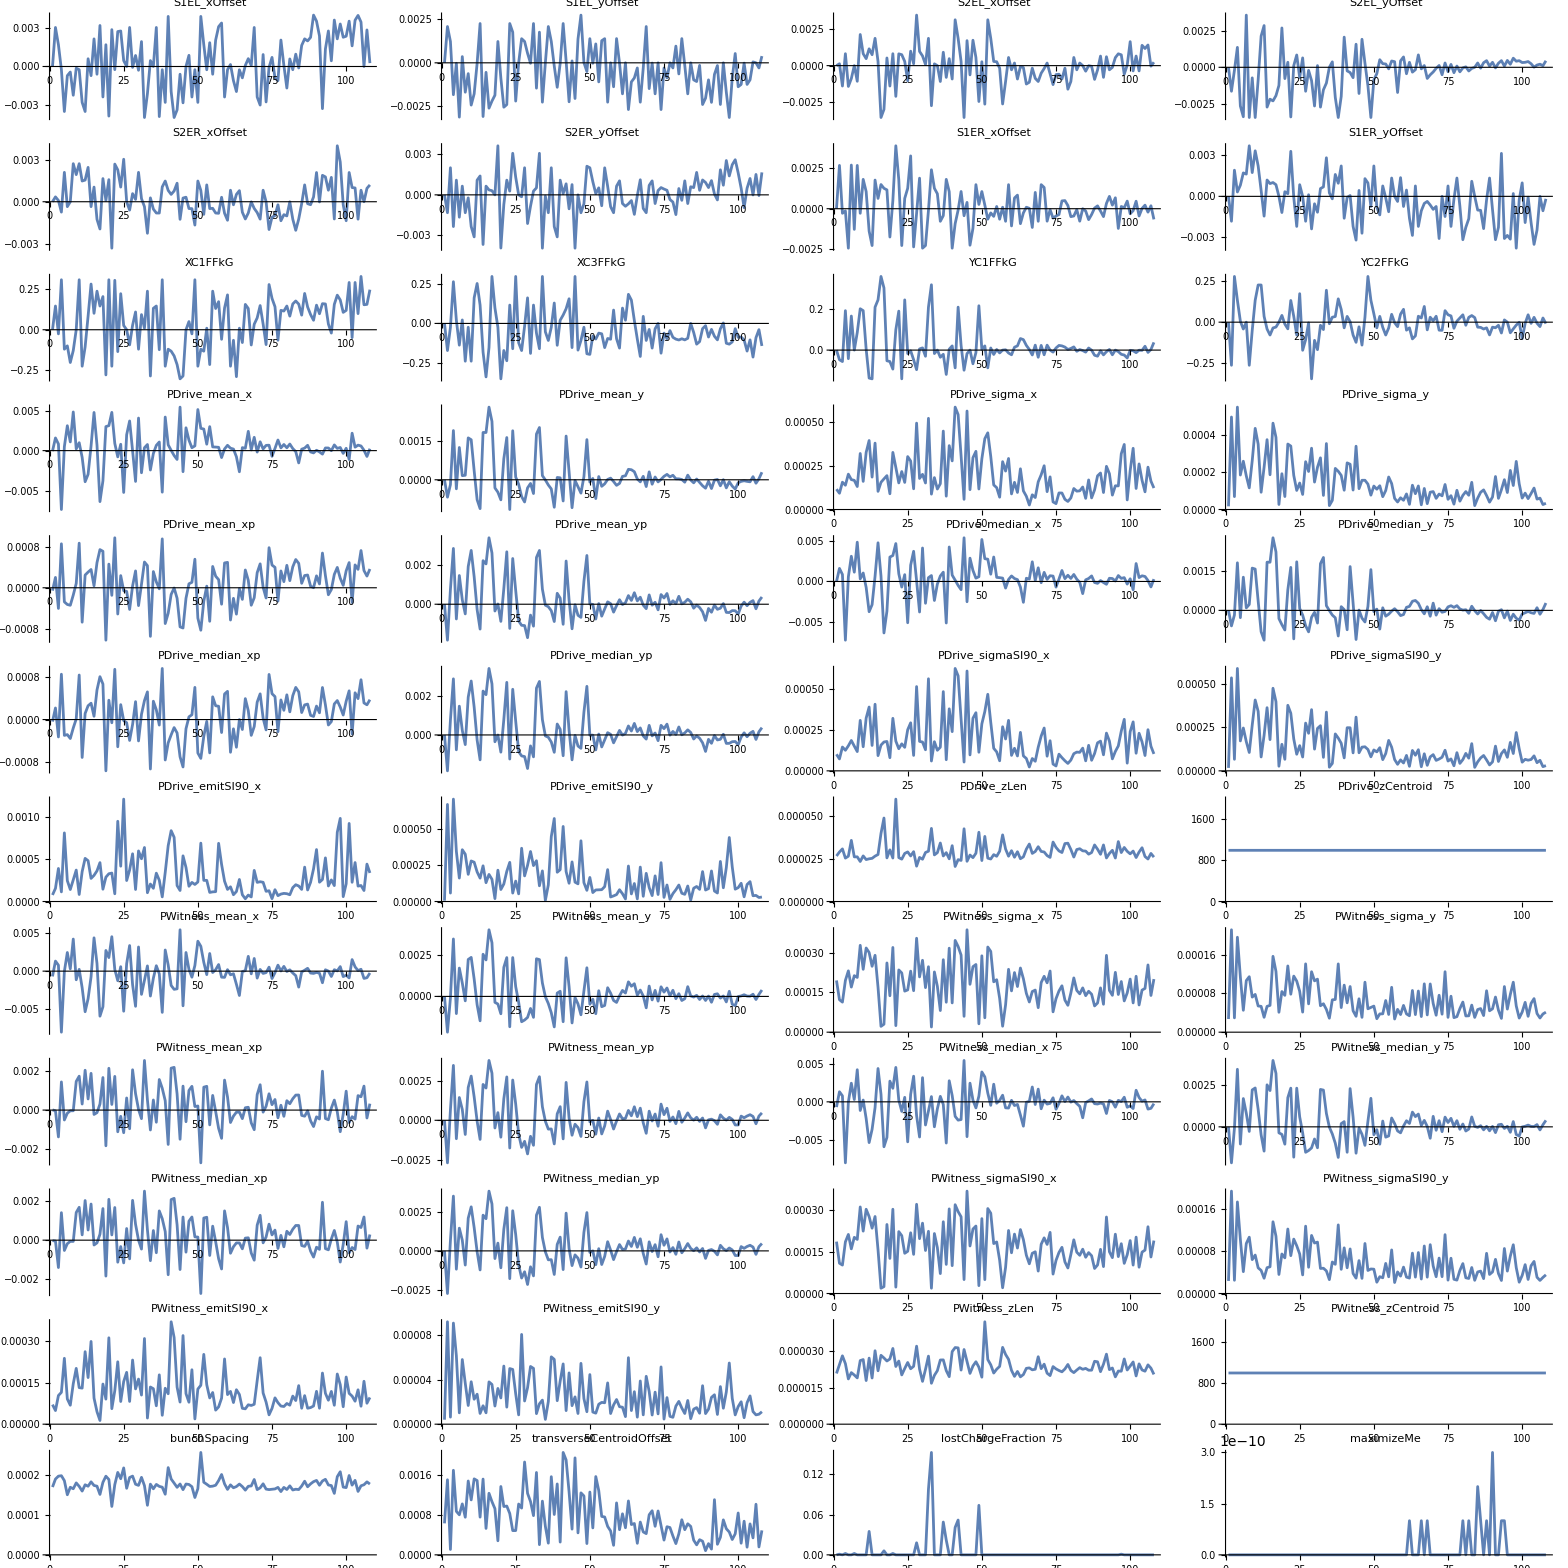

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

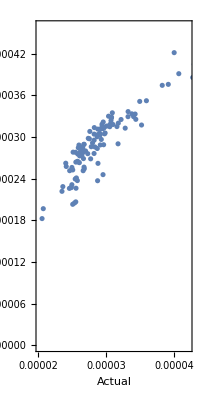

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVarsMathematica
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{S1ELxOffset→Indeterminate,S1ELyOffset→Indeterminate,S1ERxOffset→Indeterminate,S1ERyOffset→Indeterminate,S2ELxOffset→Indeterminate,S2ELyOffset→Indeterminate,S2ERxOffset→Indeterminate,S2ERyOffset→Indeterminate,XC1FFkG→Indeterminate,XC3FFkG→Indeterminate,YC1FFkG→Indeterminate,YC2FFkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
S1ELxOffset | 1 | 3.59935×10^-10 | 3.59935×10^-10 | 52.0968 | 1.28892×10^-10
S1ELyOffset | 1 | 1.23757×10^-10 | 1.23757×10^-10 | 17.9125 | 0.0000533542
S1ERxOffset | 1 | 2.32601×10^-10 | 2.32601×10^-10 | 33.6665 | 8.57999×10^-8
S1ERyOffset | 1 | 3.4387×10^-11 | 3.4387×10^-11 | 4.97716 | 0.0280368
S2ELxOffset | 1 | 1.29826×10^-9 | 1.29826×10^-9 | 187.909 | 3.07026×10^-24
S2ELyOffset | 1 | 4.656×10^-13 | 4.656×10^-13 | 0.0673906 | 0.795736
S2ERxOffset | 1 | 4.00825×10^-10 | 4.00825×10^-10 | 58.0152 | 1.9163×10^-11
S2ERyOffset | 1 | 2.65188×10^-11 | 2.65188×10^-11 | 3.83832 | 0.0530253
XC1FFkG | 1 | 1.03519×10^-11 | 1.03519×10^-11 | 1.49832 | 0.223957
XC3FFkG | 1 | 3.49311×10^-12 | 3.49311×10^-12 | 0.505591 | 0.478796
YC1FFkG | 1 | 1.66688×10^-11 | 1.66688×10^-11 | 2.41264 | 0.123685
YC2FFkG | 1 | 5.62267×10^-12 | 5.62267×10^-12 | 0.813822 | 0.369274
Error | 95 | 6.56352×10^-10 | 6.90897×10^-12 |  | 
Total | 107 | 3.16924×10^-9 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```